```mathematica
W= {{0,1,2,4},{1,0,3,5},{2,3,0,6},{4,5,6,0}}
```

{{0,1,2,4},{1,0,3,5},{2,3,0,6},{4,5,6,0}}

```mathematica
state = RandomInteger[{},4]
```

{-1,0,-1,0}

```mathematica
theta = RandomReal[{0,100},4]
```

{0.38909,2.17515,7.21081,2.0131}

```mathematica
state.W.state
```

12

```mathematica
Energy[w_,θ_][s_] := θ . s - (s . w. s/2);


UpdateState[w_,θ_][s_]:= With[{s2 = MapAt[1-#&, s, RandomInteger[{1,Length[s]}]]},
If[Energy[w,θ][s2]<Energy[w,θ][s],s2,s]]
```

```mathematica
graycode[n_]:=Map[IntegerDigits[#,2,n]&,Map[BitXor[#,Floor[#/2]]&,Range[0,2^n-1]]]
```

```mathematica
neg[n_]:=2*n-1
graycodeneg1[l_]:=Map[neg,l]
```

```mathematica
graycodeneg[n_]:=Map[graycodeneg1,graycode[n]]
```

```mathematica
ArrayPlot[NestList[UpdateState[W,theta],{0,0,1,1},100]]
```

-Graphics-

```mathematica
graycode[4]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,1},{0,0,1,0},{0,1,1,0},{0,1,1,1},{0,1,0,1},{0,1,0,0},{1,1,0,0},{1,1,0,1},{1,1,1,1},{1,1,1,0},{1,0,1,0},{1,0,1,1},{1,0,0,1},{1,0,0,0}}

```mathematica
ClearAll[W,theta]
```

```mathematica
boa[w_,θ_]:=Map[Nest[UpdateState[w,θ],#,100]&,graycode[4]]
```

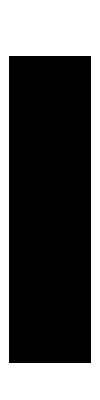

```mathematica
ArrayPlot[boa[W,theta]]
```

```mathematica
boa1[w_,θ_,n_,state_]:=Nest[UpdateState[w,θ],state,200]
```

```mathematica
boa2[w_,θ_,n_][state_] :=DeleteDuplicates[Table[boa1[w,θ,n,state],{i,100}]]
```

```mathematica
boa3[w_,θ_,n_]:={ boa2[w,θ,n][#],#}&/@graycode[n]
```

```mathematica
boa3[W,theta,4]
```

{{{{0,0,0,0}},{0,0,0,0}},{{{1,1,1,1},{0,0,0,0}},{0,0,0,1}},{{{1,1,1,1},{0,0,0,0}},{0,0,1,1}},{{{0,0,0,0},{1,1,1,1}},{0,0,1,0}},{{{1,1,1,1},{0,0,0,0}},{0,1,1,0}},{{{1,1,1,1}},{0,1,1,1}},{{{1,1,1,1}},{0,1,0,1}},{{{1,1,1,1},{0,0,0,0}},{0,1,0,0}},{{{1,1,1,1},{0,0,0,0}},{1,1,0,0}},{{{1,1,1,1}},{1,1,0,1}},{{{1,1,1,1}},{1,1,1,1}},{{{1,1,1,1},{0,0,0,0}},{1,1,1,0}},{{{1,1,1,1},{0,0,0,0}},{1,0,1,0}},{{{1,1,1,1}},{1,0,1,1}},{{{1,1,1,1}},{1,0,0,1}},{{{0,0,0,0},{1,1,1,1}},{1,0,0,0}}}

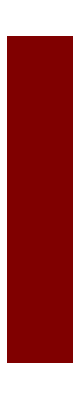

```mathematica
ArrayPlot[%]
```

```mathematica
meanboa[l_]:=Map[ReplacePart[#,1->Mean[#[[1]]]]&,l]
```

```mathematica
meanboa[boa3[W,theta,4]]
```

{{{0,0,0,0},{0,0,0,0}},{{1/2,1/2,1/2,1/2},{0,0,0,1}},{{1,1,1,1},{0,0,1,1}},{{1/2,1/2,1/2,1/2},{0,0,1,0}},{{1,1,1,1},{0,1,1,0}},{{1,1,1,1},{0,1,1,1}},{{1,1,1,1},{0,1,0,1}},{{1/2,1/2,1/2,1/2},{0,1,0,0}},{{1,1,1,1},{1,1,0,0}},{{1,1,1,1},{1,1,0,1}},{{1,1,1,1},{1,1,1,1}},{{1,1,1,1},{1,1,1,0}},{{1,1,1,1},{1,0,1,0}},{{1,1,1,1},{1,0,1,1}},{{1,1,1,1},{1,0,0,1}},{{1/2,1/2,1/2,1/2},{1,0,0,0}}}